# Modified Einstein

Das gute alte, mit vielen Notebooks diskutierte A^-2-Thema, noch einmal in einem neuen Notebook aufgerollt, basierend auf Calc17, also den Modified-GUP-Rechnungen. Interessanterweise ist ja die GUP-FT fast die gleiche wie die Holographie-FT.

## Definitionen

Wir definieren v=vEff und v_+, v_- jetzt entsprechend der Definitionen in der Masterarbeit.

Unsere Fouriertransformation geht von a → b. Je nach Richtung der Fouriertransformation ist a=z, b=q oder andersrum.

```mathematica
holo[z_,n_]=1/(1+1/z^(2+n));
A2Vorfaktor = 1/(2Pi)^(3+n)I/(2 p)1/L^2;
vSide[h_,z_,n_, side_]:= If[side>0,D[h[z,n],z]/z,(D[h[z,n],z]/.{z-> -z})/z] //FullSimplify
vEff[h_,z_,n_] := vSide[h,z,n,+1]HeavisideTheta[z] + vSide[h,z,n,-1]HeavisideTheta[-z]
```

```mathematica
vEff[holo,z,n] // FullSimplify // TraditionalForm
```

((n+2) z z^n)/((z^(n+2)+1)^2)-((n+2) -z (-z)^n)/(((-z)^(n+2)+1)^2)

```mathematica
V[hGUP,z,n] // FullSimplify
vSide[hGUP,z,n,+1]
vSide[hGUP,z,n,-1]
```

V[hGUP,z,n]

(hGUP^(1,0)[z,n])/z

(hGUP^(1,0)[-z,n])/z

```mathematica
integralSchluss = unten;
integralSchlussMglkten = {oben, unten};
polChoices = {Im[#]≥  0&, Im[#]≤ 0&};
resVorzeichen = {+1, -1};
integralSchlussWahl=First@First@Position[integralSchlussMglkten,integralSchluss];
```

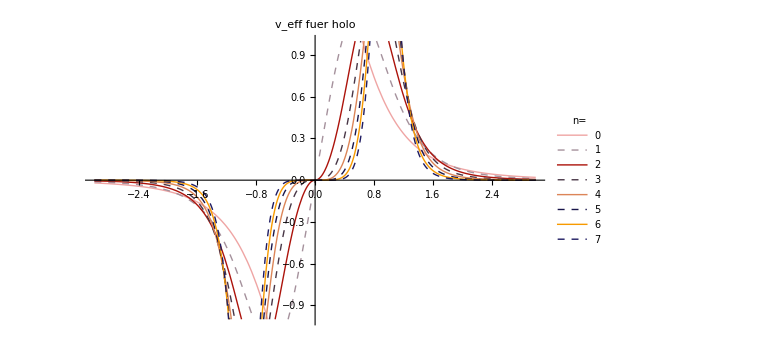

```mathematica
Plot[Table[vEff[holo,z,n], {n,0,7}]//Evaluate,
{z,-3,3},
PlotStyle->(Riffle[#,{Dashed,#}&/@Reverse[#]]& [ColorData[9,"ColorList"]]),
PlotLegends-> LineLegend[Table[n,{n,0,7}],LegendLabel-> "n="],
PlotLabel-> "v_eff fuer "<>ToString@holo,
PlotRange-> {-1,1},
ImageSize-> Large]
```

## Polstellen extrahieren

Auch hier Code komplett kopiert von Calc17/GUP.

```mathematica
ReduceToSolutions[reduceResult_, extractVariable_] := Cases[reduceResult,Equal[extractVariable, value_]-> value, 100]
polReduce[h_,n_, side_] := Reduce[Denominator@vSide[h,z,n, side]==0,z]
polstellenSide[h_,n_,side_] := polReduce[h,n,side]~ ReduceToSolutions ~ z
polstellen[h_,n_] := Join@@(Select[polstellenSide[h,n,#[[1]]], #[[2]]]&) /@ {
+1 ->  (Re[#] ≥ 0&),
-1 -> (Re[#] ≤ 0&)
}
mitgenommenePolstellen[h_,n_] := Select[polstellen[h,n], polChoices⟦integralSchlussWahl⟧]
```

```mathematica
Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n", "# unique poles", "# poles","Unique Poles Holography"}},
Table[{n,
Length@Union@polstellen[holo,n],
Length@polstellen[holo,n],
Union@polstellen[holo,n] // Sort
},{n,0,7}]},
Frame -> All, Alignment-> {Left,Left}]
```

n | # unique poles | # poles | Unique Poles Holography
0 | 2 | 4 | {-ⅈ,ⅈ}
1 | 4 | 4 | {-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)}
2 | 4 | 4 | {-(-1)^(1/4),(-1)^(1/4),-(-1)^(3/4),(-1)^(3/4)}
3 | 4 | 4 | {-(-1)^(1/5),(-1)^(1/5),-(-1)^(4/5),(-1)^(4/5)}
4 | 6 | 8 | {-ⅈ,ⅈ,-(-1)^(1/6),(-1)^(1/6),-(-1)^(5/6),(-1)^(5/6)}
5 | 8 | 8 | {-(-1)^(1/7),(-1)^(1/7),-(-1)^(3/7),(-1)^(3/7),-(-1)^(4/7),(-1)^(4/7),-(-1)^(6/7),(-1)^(6/7)}
6 | 8 | 8 | {-(-1)^(1/8),(-1)^(1/8),-(-1)^(3/8),(-1)^(3/8),-(-1)^(5/8),(-1)^(5/8),-(-1)^(7/8),(-1)^(7/8)}
7 | 8 | 8 | {-(-1)^(1/9),(-1)^(1/9),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),-(-1)^(8/9),(-1)^(8/9)}

## Integralberechnung

```mathematica
(* Holo-Modell: (-1) weil untenrum geschlossen *)
IntegralResidueList[h_,n_] := 
(2 Pi I) * resVorzeichen⟦integralSchlussWahl⟧  * Residue[vSide[h,z, n, Sign@Re@#] * Exp[-I q z], {z,#}]& /@ mitgenommenePolstellen[h,n]
IntegralValue[h_,n_] := Total@IntegralResidueList[h,n]
(* A^-2 ist gegeben durch: Integralvorfaktoren, V-Vorfaktoren. *)
AValue[h_,n_] :=  A2Vorfaktor  IntegralValue[h,n]
```

```mathematica
With[{h=holo},
Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n", "# poles","Wert für A(p)"}},
Table[{n,
Length@mitgenommenePolstellen[h,n],
AValue[holo,n]  /. {q-> p L} // Simplify,
AValue[holo,n] /. {q-> p L} // Simplify //ComplexExpand 
(*AValue[n]//ComplexExpand // FullSimplify*)
},{n,0,8}]},
Frame -> All, Alignment-> {Left,Left}]]
```

n | # poles | Wert für A(p) | 
0 | 2 | -(ⅈ ⅇ^(-L p) (1+L p))/(8 L^2 p π^2) | ⅈ (-ⅇ^(-L p)/(8 L π^2)-ⅇ^(-L p)/(8 L^2 p π^2))
1 | 2 | -(ⅈ ⅇ^(-(-1)^(1/6) L p) ((-1)^(5/6)-L p+ⅇ^(ⅈ L p) ((-1)^(1/6)+L p)))/(48 L^2 p π^3) | (ⅇ^(-1/2 √3 L p) Cos[(L p)/2])/(96 L^2 p π^3)+(ⅇ^(-1/2 √3 L p) Cos[(L p)/2] Cos[L p])/(96 L^2 p π^3)+(ⅇ^(-1/2 √3 L p) Sin[(L p)/2])/(48 L π^3)+(ⅇ^(-1/2 √3 L p) Sin[(L p)/2])/(32 √3 L^2 p π^3)-(ⅇ^(-1/2 √3 L p) Cos[L p] Sin[(L p)/2])/(48 L π^3)-(ⅇ^(-1/2 √3 L p) Cos[L p] Sin[(L p)/2])/(32 √3 L^2 p π^3)+(ⅇ^(-1/2 √3 L p) Cos[(L p)/2] Sin[L p])/(48 L π^3)+(ⅇ^(-1/2 √3 L p) Cos[(L p)/2] Sin[L p])/(32 √3 L^2 p π^3)+(ⅇ^(-1/2 √3 L p) Sin[(L p)/2] Sin[L p])/(96 L^2 p π^3)+ⅈ ((ⅇ^(-1/2 √3 L p) Cos[(L p)/2])/(48 L π^3)+(ⅇ^(-1/2 √3 L p) Cos[(L p)/2])/(32 √3 L^2 p π^3)-(ⅇ^(-1/2 √3 L p) Cos[(L p)/2] Cos[L p])/(48 L π^3)-(ⅇ^(-1/2 √3 L p) Cos[(L p)/2] Cos[L p])/(32 √3 L^2 p π^3)-(ⅇ^(-1/2 √3 L p) Sin[(L p)/2])/(96 L^2 p π^3)-(ⅇ^(-1/2 √3 L p) Cos[L p] Sin[(L p)/2])/(96 L^2 p π^3)+(ⅇ^(-1/2 √3 L p) Cos[(L p)/2] Sin[L p])/(96 L^2 p π^3)-(ⅇ^(-1/2 √3 L p) Sin[(L p)/2] Sin[L p])/(48 L π^3)-(ⅇ^(-1/2 √3 L p) Sin[(L p)/2] Sin[L p])/(32 √3 L^2 p π^3))
2 | 2 | (ⅇ^(-(-1)^(1/4) L p) ((-1)^(1/4)+ⅈ L p-ⅇ^(ⅈ √2 L p) ((-1)^(3/4)+ⅈ L p)))/(128 L^2 p π^4) | (ⅇ^(-(L p)/(√2)) Cos[(L p)/(√2)])/(128 √2 L^2 p π^4)+(ⅇ^(-(L p)/(√2)) Cos[(L p)/(√2)] Cos[√2 L p])/(128 √2 L^2 p π^4)+(ⅇ^(-(L p)/(√2)) Sin[(L p)/(√2)])/(128 L π^4)+(ⅇ^(-(L p)/(√2)) Sin[(L p)/(√2)])/(128 √2 L^2 p π^4)-(ⅇ^(-(L p)/(√2)) Cos[√2 L p] Sin[(L p)/(√2)])/(128 L π^4)-(ⅇ^(-(L p)/(√2)) Cos[√2 L p] Sin[(L p)/(√2)])/(128 √2 L^2 p π^4)+(ⅇ^(-(L p)/(√2)) Cos[(L p)/(√2)] Sin[√2 L p])/(128 L π^4)+(ⅇ^(-(L p)/(√2)) Cos[(L p)/(√2)] Sin[√2 L p])/(128 √2 L^2 p π^4)+(ⅇ^(-(L p)/(√2)) Sin[(L p)/(√2)] Sin[√2 L p])/(128 √2 L^2 p π^4)+ⅈ ((ⅇ^(-(L p)/(√2)) Cos[(L p)/(√2)])/(128 L π^4)+(ⅇ^(-(L p)/(√2)) Cos[(L p)/(√2)])/(128 √2 L^2 p π^4)-(ⅇ^(-(L p)/(√2)) Cos[(L p)/(√2)] Cos[√2 L p])/(128 L π^4)-(ⅇ^(-(L p)/(√2)) Cos[(L p)/(√2)] Cos[√2 L p])/(128 √2 L^2 p π^4)-(ⅇ^(-(L p)/(√2)) Sin[(L p)/(√2)])/(128 √2 L^2 p π^4)-(ⅇ^(-(L p)/(√2)) Cos[√2 L p] Sin[(L p)/(√2)])/(128 √2 L^2 p π^4)+(ⅇ^(-(L p)/(√2)) Cos[(L p)/(√2)] Sin[√2 L p])/(128 √2 L^2 p π^4)-(ⅇ^(-(L p)/(√2)) Sin[(L p)/(√2)] Sin[√2 L p])/(128 L π^4)-(ⅇ^(-(L p)/(√2)) Sin[(L p)/(√2)] Sin[√2 L p])/(128 √2 L^2 p π^4))
3 | 2 | -(ⅈ ⅇ^(-(-1)^(3/10) L p) ((-1)^(7/10)-L p+ⅇ^((-1)^(3/10) (1+(-1)^(2/5)) L p) ((-1)^(3/10)+L p)))/(320 L^2 p π^5) | (ⅇ^(-√(5/8-(√5)/8) L p) Cos[1/4 (-1-√5) L p])/(1280 L^2 p π^5)+(ⅇ^(-√(5/8-(√5)/8) L p) Cos[1/4 (-1-√5) L p])/(256 √5 L^2 p π^5)+1/(1280 L^2 p π^5)ⅇ^(-√(5/8-(√5)/8) L p+(-1/4 √(5/8+(√5)/8) (1+√5)+√(5/8-(√5)/8) (1+1/4 (-1+√5))) L p) Cos[1/4 (-1-√5) L p] Cos[(1/2+(√5)/4+√((5/8-(√5)/8) (5/8+(√5)/8))) L p]+1/(256 √5 L^2 p π^5)ⅇ^(-√(5/8-(√5)/8) L p+(-1/4 √(5/8+(√5)/8) (1+√5)+√(5/8-(√5)/8) (1+1/4 (-1+√5))) L p) Cos[1/4 (-1-√5) L p] Cos[(1/2+(√5)/4+√((5/8-(√5)/8) (5/8+(√5)/8))) L p]-(ⅇ^(-√(5/8-(√5)/8) L p) Sin[1/4 (-1-√5) L p])/(320 L π^5)-(√(5/8-(√5)/8) ⅇ^(-√(5/8-(√5)/8) L p) Sin[1/4 (-1-√5) L p])/(320 L^2 p π^5)+1/(320 L π^5)ⅇ^(-√(5/8-(√5)/8) L p+(-1/4 √(5/8+(√5)/8) (1+√5)+√(5/8-(√5)/8) (1+1/4 (-1+√5))) L p) Cos[(1/2+(√5)/4+√((5/8-(√5)/8) (5/8+(√5)/8))) L p] Sin[1/4 (-1-√5) L p]+1/(320 L^2 p π^5)√(5/8-(√5)/8) ⅇ^(-√(5/8-(√5)/8) L p+(-1/4 √(5/8+(√5)/8) (1+√5)+√(5/8-(√5)/8) (1+1/4 (-1+√5))) L p) Cos[(1/2+(√5)/4+√((5/8-(√5)/8) (5/8+(√5)/8))) L p] Sin[1/4 (-1-√5) L p]+1/(320 L π^5)ⅇ^(-√(5/8-(√5)/8) L p+(-1/4 √(5/8+(√5)/8) (1+√5)+√(5/8-(√5)/8) (1+1/4 (-1+√5))) L p) Cos[1/4 (-1-√5) L p] Sin[(1/2+(√5)/4+√((5/8-(√5)/8) (5/8+(√5)/8))) L p]+1/(320 L^2 p π^5)√(5/8-(√5)/8) ⅇ^(-√(5/8-(√5)/8) L p+(-1/4 √(5/8+(√5)/8) (1+√5)+√(5/8-(√5)/8) (1+1/4 (-1+√5))) L p) Cos[1/4 (-1-√5) L p] Sin[(1/2+(√5)/4+√((5/8-(√5)/8) (5/8+(√5)/8))) L p]-1/(1280 L^2 p π^5)ⅇ^(-√(5/8-(√5)/8) L p+(-1/4 √(5/8+(√5)/8) (1+√5)+√(5/8-(√5)/8) (1+1/4 (-1+√5))) L p) Sin[1/4 (-1-√5) L p] Sin[(1/2+(√5)/4+√((5/8-(√5)/8) (5/8+(√5)/8))) L p]-1/(256 √5 L^2 p π^5)ⅇ^(-√(5/8-(√5)/8) L p+(-1/4 √(5/8+(√5)/8) (1+√5)+√(5/8-(√5)/8) (1+1/4 (-1+√5))) L p) Sin[1/4 (-1-√5) L p] Sin[(1/2+(√5)/4+√((5/8-(√5)/8) (5/8+(√5)/8))) L p]+ⅈ ((ⅇ^(-√(5/8-(√5)/8) L p) Cos[1/4 (-1-√5) L p])/(320 L π^5)+(√(5/8-(√5)/8) ⅇ^(-√(5/8-(√5)/8) L p) Cos[1/4 (-1-√5) L p])/(320 L^2 p π^5)-1/(320 L π^5)ⅇ^(-√(5/8-(√5)/8) L p+(-1/4 √(5/8+(√5)/8) (1+√5)+√(5/8-(√5)/8) (1+1/4 (-1+√5))) L p) Cos[1/4 (-1-√5) L p] Cos[(1/2+(√5)/4+√((5/8-(√5)/8) (5/8+(√5)/8))) L p]-1/(320 L^2 p π^5)√(5/8-(√5)/8) ⅇ^(-√(5/8-(√5)/8) L p+(-1/4 √(5/8+(√5)/8) (1+√5)+√(5/8-(√5)/8) (1+1/4 (-1+√5))) L p) Cos[1/4 (-1-√5) L p] Cos[(1/2+(√5)/4+√((5/8-(√5)/8) (5/8+(√5)/8))) L p]+(ⅇ^(-√(5/8-(√5)/8) L p) Sin[1/4 (-1-√5) L p])/(1280 L^2 p π^5)+(ⅇ^(-√(5/8-(√5)/8) L p) Sin[1/4 (-1-√5) L p])/(256 √5 L^2 p π^5)+1/(1280 L^2 p π^5)ⅇ^(-√(5/8-(√5)/8) L p+(-1/4 √(5/8+(√5)/8) (1+√5)+√(5/8-(√5)/8) (1+1/4 (-1+√5))) L p) Cos[(1/2+(√5)/4+√((5/8-(√5)/8) (5/8+(√5)/8))) L p] Sin[1/4 (-1-√5) L p]+1/(256 √5 L^2 p π^5)ⅇ^(-√(5/8-(√5)/8) L p+(-1/4 √(5/8+(√5)/8) (1+√5)+√(5/8-(√5)/8) (1+1/4 (-1+√5))) L p) Cos[(1/2+(√5)/4+√((5/8-(√5)/8) (5/8+(√5)/8))) L p] Sin[1/4 (-1-√5) L p]+1/(1280 L^2 p π^5)ⅇ^(-√(5/8-(√5)/8) L p+(-1/4 √(5/8+(√5)/8) (1+√5)+√(5/8-(√5)/8) (1+1/4 (-1+√5))) L p) Cos[1/4 (-1-√5) L p] Sin[(1/2+(√5)/4+√((5/8-(√5)/8) (5/8+(√5)/8))) L p]+1/(256 √5 L^2 p π^5)ⅇ^(-√(5/8-(√5)/8) L p+(-1/4 √(5/8+(√5)/8) (1+√5)+√(5/8-(√5)/8) (1+1/4 (-1+√5))) L p) Cos[1/4 (-1-√5) L p] Sin[(1/2+(√5)/4+√((5/8-(√5)/8) (5/8+(√5)/8))) L p]+1/(320 L π^5)ⅇ^(-√(5/8-(√5)/8) L p+(-1/4 √(5/8+(√5)/8) (1+√5)+√(5/8-(√5)/8) (1+1/4 (-1+√5))) L p) Sin[1/4 (-1-√5) L p] Sin[(1/2+(√5)/4+√((5/8-(√5)/8) (5/8+(√5)/8))) L p]+1/(320 L^2 p π^5)√(5/8-(√5)/8) ⅇ^(-√(5/8-(√5)/8) L p+(-1/4 √(5/8+(√5)/8) (1+√5)+√(5/8-(√5)/8) (1+1/4 (-1+√5))) L p) Sin[1/4 (-1-√5) L p] Sin[(1/2+(√5)/4+√((5/8-(√5)/8) (5/8+(√5)/8))) L p])
4 | 4 | -(ⅈ ⅇ^(-(1+(-1)^(1/3)) L p) (ⅇ^(L p) ((-1)^(2/3)-L p)+2 ⅇ^((-1)^(1/3) L p) (1+L p)+ⅇ^((1+ⅈ √3) L p) ((-1)^(1/3)+L p)))/(768 L^2 p π^6) | (ⅇ^(-(L p)/2) Cos[1/2 √3 L p])/(512 √3 L^2 p π^6)+(ⅇ^(-(L p)/2) Cos[1/2 √3 L p] Cos[√3 L p])/(512 √3 L^2 p π^6)+(ⅇ^(-(L p)/2) Sin[1/2 √3 L p])/(768 L π^6)+(ⅇ^(-(L p)/2) Sin[1/2 √3 L p])/(1536 L^2 p π^6)-(ⅇ^(-(L p)/2) Cos[√3 L p] Sin[1/2 √3 L p])/(768 L π^6)-(ⅇ^(-(L p)/2) Cos[√3 L p] Sin[1/2 √3 L p])/(1536 L^2 p π^6)+(ⅇ^(-(L p)/2) Cos[1/2 √3 L p] Sin[√3 L p])/(768 L π^6)+(ⅇ^(-(L p)/2) Cos[1/2 √3 L p] Sin[√3 L p])/(1536 L^2 p π^6)+(ⅇ^(-(L p)/2) Sin[1/2 √3 L p] Sin[√3 L p])/(512 √3 L^2 p π^6)+ⅈ ((ⅇ^(-(L p)/2) Cos[1/2 √3 L p])/(768 L π^6)+(ⅇ^(-(L p)/2) Cos[1/2 √3 L p])/(1536 L^2 p π^6)-(ⅇ^(-L p) Cos[1/2 √3 L p]^2)/(384 L π^6)-(ⅇ^(-L p) Cos[1/2 √3 L p]^2)/(384 L^2 p π^6)-(ⅇ^(-(L p)/2) Cos[1/2 √3 L p] Cos[√3 L p])/(768 L π^6)-(ⅇ^(-(L p)/2) Cos[1/2 √3 L p] Cos[√3 L p])/(1536 L^2 p π^6)-(ⅇ^(-(L p)/2) Sin[1/2 √3 L p])/(512 √3 L^2 p π^6)-(ⅇ^(-(L p)/2) Cos[√3 L p] Sin[1/2 √3 L p])/(512 √3 L^2 p π^6)-(ⅇ^(-L p) Sin[1/2 √3 L p]^2)/(384 L π^6)-(ⅇ^(-L p) Sin[1/2 √3 L p]^2)/(384 L^2 p π^6)+(ⅇ^(-(L p)/2) Cos[1/2 √3 L p] Sin[√3 L p])/(512 √3 L^2 p π^6)-(ⅇ^(-(L p)/2) Sin[1/2 √3 L p] Sin[√3 L p])/(768 L π^6)-(ⅇ^(-(L p)/2) Sin[1/2 √3 L p] Sin[√3 L p])/(1536 L^2 p π^6))
5 | 4 | 1/(1792 L^2 p π^7)ⅈ (-ⅇ^((-1)^(13/14) L p) ((-1)^(1/14)+L p)-ⅇ^((-1)^(9/14) L p) ((-1)^(5/14)+L p)+ⅇ^(-(-1)^(5/14) L p) (-(-1)^(9/14)+L p)+ⅇ^(-(-1)^(1/14) L p) (-(-1)^(13/14)+L p)) | (ⅇ^(-L p Sin[π/7]) Cos[π/7] Cos[L p Cos[π/7]])/(896 L^2 p π^7)+(ⅇ^(-L p Cos[π/14]) Cos[L p Sin[π/14]] Sin[π/14])/(896 L^2 p π^7)+(ⅇ^(-L p Sin[π/7]) Sin[L p Cos[π/7]])/(896 L π^7)+(ⅇ^(-L p Sin[π/7]) Sin[π/7] Sin[L p Cos[π/7]])/(896 L^2 p π^7)+(ⅇ^(-L p Cos[π/14]) Sin[L p Sin[π/14]])/(896 L π^7)+(ⅇ^(-L p Cos[π/14]) Cos[π/14] Sin[L p Sin[π/14]])/(896 L^2 p π^7)
6 | 4 | 1/(4096 L^2 p π^8)ⅈ (-ⅇ^((-1)^(7/8) L p) ((-1)^(1/8)+L p)-ⅇ^((-1)^(5/8) L p) ((-1)^(3/8)+L p)+ⅇ^(-(-1)^(3/8) L p) (-(-1)^(5/8)+L p)+ⅇ^(-(-1)^(1/8) L p) (-(-1)^(7/8)+L p)) | (ⅇ^(-L p Sin[π/8]) Cos[π/8] Cos[L p Cos[π/8]])/(2048 L^2 p π^8)+(ⅇ^(-L p Cos[π/8]) Cos[L p Sin[π/8]] Sin[π/8])/(2048 L^2 p π^8)+(ⅇ^(-L p Sin[π/8]) Sin[L p Cos[π/8]])/(2048 L π^8)+(ⅇ^(-L p Sin[π/8]) Sin[π/8] Sin[L p Cos[π/8]])/(2048 L^2 p π^8)+(ⅇ^(-L p Cos[π/8]) Sin[L p Sin[π/8]])/(2048 L π^8)+(ⅇ^(-L p Cos[π/8]) Cos[π/8] Sin[L p Sin[π/8]])/(2048 L^2 p π^8)
7 | 4 | 1/(9216 L^2 p π^9)ⅈ (-ⅇ^((-1)^(5/6) L p) ((-1)^(1/6)+L p)-ⅇ^((-1)^(11/18) L p) ((-1)^(7/18)+L p)+ⅇ^(-(-1)^(7/18) L p) (-(-1)^(11/18)+L p)+ⅇ^(-(-1)^(1/6) L p) (-(-1)^(5/6)+L p)) | (ⅇ^(-1/2 √3 L p) Cos[(L p)/2])/(9216 L^2 p π^9)+(ⅇ^(-L p Sin[π/9]) Cos[π/9] Cos[L p Cos[π/9]])/(4608 L^2 p π^9)+(ⅇ^(-1/2 √3 L p) Sin[(L p)/2])/(4608 L π^9)+(ⅇ^(-1/2 √3 L p) Sin[(L p)/2])/(3072 √3 L^2 p π^9)+(ⅇ^(-L p Sin[π/9]) Sin[L p Cos[π/9]])/(4608 L π^9)+(ⅇ^(-L p Sin[π/9]) Sin[π/9] Sin[L p Cos[π/9]])/(4608 L^2 p π^9)
8 | 6 | 1/(20480 L^2 p π^10)ⅈ (-2 ⅇ^(-L p) (1+L p)-ⅇ^((-1)^(4/5) L p) ((-1)^(1/5)+L p)-ⅇ^((-1)^(3/5) L p) ((-1)^(2/5)+L p)+ⅇ^(-(-1)^(2/5) L p) (-(-1)^(3/5)+L p)+ⅇ^(-(-1)^(1/5) L p) (-(-1)^(4/5)+L p)) | ⅈ (-ⅇ^(-L p)/(10240 L π^10)-ⅇ^(-L p)/(10240 L^2 p π^10))+(√(5/8-(√5)/8) ⅇ^(1/4 (-1-√5) L p) Cos[√(5/8-(√5)/8) L p])/(10240 L^2 p π^10)+(√(5/8+(√5)/8) ⅇ^(1/4 (1-√5) L p) Cos[√(5/8+(√5)/8) L p])/(10240 L^2 p π^10)+(ⅇ^(1/4 (-1-√5) L p) Sin[√(5/8-(√5)/8) L p])/(10240 L π^10)+(ⅇ^(1/4 (-1-√5) L p) Sin[√(5/8-(√5)/8) L p])/(40960 L^2 p π^10)+(ⅇ^(1/4 (-1-√5) L p) Sin[√(5/8-(√5)/8) L p])/(8192 √5 L^2 p π^10)+(ⅇ^(1/4 (1-√5) L p) Sin[√(5/8+(√5)/8) L p])/(10240 L π^10)-(ⅇ^(1/4 (1-√5) L p) Sin[√(5/8+(√5)/8) L p])/(40960 L^2 p π^10)+(ⅇ^(1/4 (1-√5) L p) Sin[√(5/8+(√5)/8) L p])/(8192 √5 L^2 p π^10)

```mathematica
data =Table[AValue[holo,n],{n,0,4}]//.{q-> p L,L-> 1}//ComplexExpand;
```

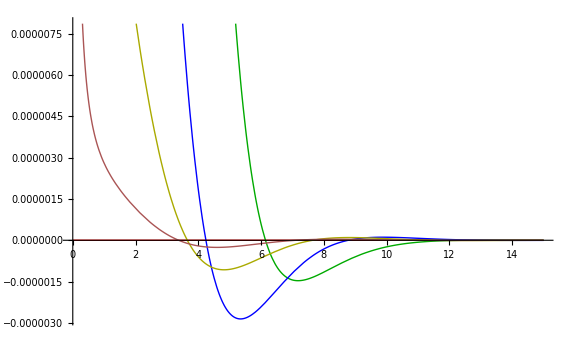
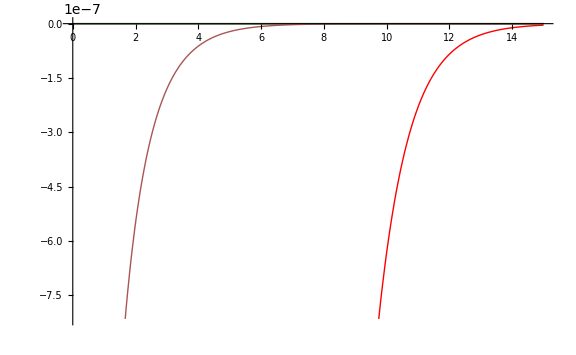

```mathematica
Plot[
Evaluate[#/@data],
{p,0,15},
PlotStyle-> (*Flatten[{#,{Dashed,#}}&/@*){Red, Darker@Green, Blue, Darker@Yellow, Darker@Pink}(*,1]*),
ImageSize-> Large
]&/@ {Re,Im}
```